# Financial Econometrics I

Modeling Volatility

## (Lecture 4)

Summer Semester 2025/2026 by Lukas Vacha

* If viewed in .pdf format - for full functionality use Mathematica 7 (or higher) notebook (.nb) version of this .pdf

## Characteristics of Volatility

Volatility is one of the most important concepts in finance, as it measures the risk of financial assets. Volatility is not directly observable, it can be just estimated. It has some important characteristics:

volatility clusters - After a large (small) price change a large (small) price change tends to occur.

volatility does not diverge to infinity - it varies within some fixed range.

negative and positive price shocks tend to have different impacts on volatility (leverage effect)

heavy-tailed, non-Gaussian distribution

### Historical Volatility

Most straightforward way to measure volatility is to estimate time-series of variance on "rolling samples" For zero-mean variable, this would be:

σ_t^2=(r_(t-1)^2+r_(t-2)^2+...+r_(t-q)^2)/q,

where 𝓆 is the latest observation used. This method may produce abrupt changes in estimates.

### Exponential volatility

Alternatively, exponential moving average (EMA) estimator of volatility can be used. It uses all data points, and recent observations carry larger weights. (weights are exponentially decreasing):

σ_t^2=(∑_(τ=1)^m λ^(τ-1)r_(t-1-τ)^2)/(1+λ+λ^1+...+λ^(m-1)),

finally we get (we derive it next week):

σ_t^2=(1-λ)r_(t-1)^2+λσ_(t-1)^2,

where initial value could be unconditional variance in a historical sample. In most financial applications, λ=0.94 is used.

### Example on S&P 500 index data

Note that characteristics of volatility can be observed from returns of S&P 500. Moreover, ACF plot suggests us, that returns are not serially correlated, but ACF plot of squared returns shows, that they are not independent. By modeling volatility, we will attempt to capture this kind of dependence.

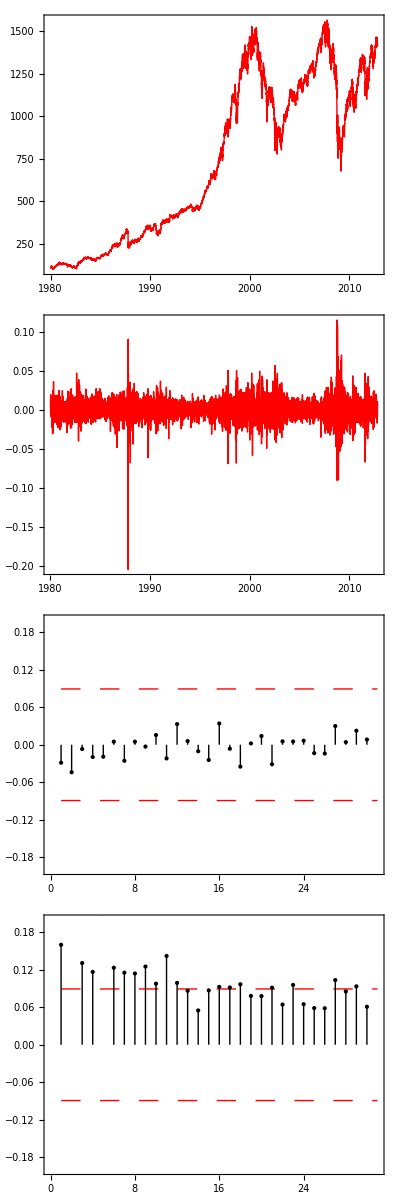

### Conditional Standard Deviation estimated by EMA (or EWMA)

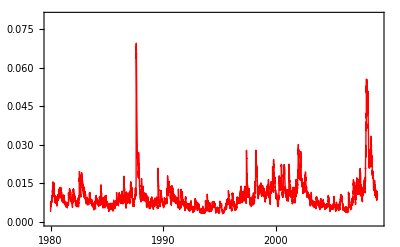
-Graphics-S&P standard deviation estimate with EMA (λ=0.9)

## Conditional Heteroscedastic Models

Log returns of an asset at time is either serially uncorrelated, or with minor lower order serial correlations, but it is dependent. Conditional heteroscedastic models are used for modeling σ_t^2 as volatility estimate by "allowing" heteroscedasticity (time-variation) and capturing that dependence.

## ARCH(1)

The first model that provides a systematic framework for volatility modeling is Autoregressive conditional heteroscedasticity (ARCH) model. ARCH(1) model is most common from ARCH(𝓂) models in financial theory. Basic idea is that the mean-corrected return is serially uncorrelated, but dependent, and that the dependence can be described by a simple function of lagged values:

r_t= μ_t+a_t
a_t=σ_t ϵ_t
σ_t^2=α_0+α_1 a_(t-1)^2

Where a_t is mean corrected return and α_0>0, α_1≥0. 
Unconditional mean of a_t is zero, unconditional variance is α_0/(1-α_1). 
The process is stationary, if α_1<1, the fourth moment is finite if 3 α_1^2<1.

### Kurtosis of ARCH(1) processes

The fourth moment of ARCH(1) process:

E[ϵ_t^4]=(3 α_0^2)/(1-α_1)^2(1-α_1^2)/(1-3 α_1^2), with 3 α_1^2<1

kurt(ϵ_t)=E[ϵ_t^4]/(E[ϵ_t^2]^2)=3(1-α_1^2)/(1-3 α_1^2)⩾3

```mathematica
Example: Subscript[α, 1]=0.1
-Graphics-
```

```mathematica
Example: Subscript[α, 1]=0.4
-Graphics-
```

```mathematica
Example: Subscript[α, 1]=0.5
```

```mathematica
Example: Subscript[α, 1]=0.9
-Graphics-
```

### Examples of ARCH(1) artificial processes

```mathematica
Manipulate[
SeedRandom[seed];
earch=RandomReal[NormalDistribution[0,1],500];
arch=Table[1,{500}];archa=Table[1,{500}];
arch[[1]]=Variance[earch];archa[[1]]=Sqrt[arch[[1]]] earch[[1]];
Do[arch[[i]]=paramp0+paramp1 archa[[i-1]]^2;
archa[[i]]=Sqrt[arch[[i]]] earch[[i]];
,{i,2,Length[earch]}];
acfarch=CorrelationFunction[arch^2,{30}];
stdevarch=2/Sqrt[500];
pacfarch=PartialCorrelationFunction[arch^2,{30}];
ListPlot[If[type==="Sample ARCH(1)",archa,
If[type==="ARCH(1) volatility",arch,
If[type==="ACF function of a_t^2",{Table[z=stdevarch,{z,0,30}],Table[z=-stdevarch,{z,0,30}],acfarch},
{Table[z=stdevarch,{z,0,30}],Table[z=-stdevarch,{z,0,30}],pacfarch}]]],
Joined->{True,True,False},Frame->True,Filling->If[type=!="Sample ARCH(1)",If[type=!="ARCH(1) volatility",{3-> Axis},None],None],FillingStyle->{3->Black},PlotStyle->If[type=!="Sample ARCH(1)",If[type=!="ARCH(1) volatility",
{{Dashing[Large], Thickness[Medium], Red}, {Dashing[Large], Thickness[Medium], Red}, Black},{Thickness[Medium], Red}],{Thickness[Medium], Red}]
,PlotRange->If[type==="Sample ARCH(1)",{-10,10},If[type==="ARCH(1) volatility",All,{-0.5,0.5}]]],
{{type,"Sample ARCH(1)",""},{"Sample ARCH(1)","ARCH(1) volatility"}},Delimiter,
{{type,"Sample ARCH(1)",""},{"ACF function of a_t^2","PACF function of a_t^2"}},Delimiter,
{{paramp0,0.5,"α_0"},0.1,2,Appearance->"Labeled"},{{paramp1,0.5,"α_1"},0,1,Appearance->"Labeled"},Delimiter,{{seed,77777,"New Random Case"},10000,999999,1}]
```

## ARCH(𝓂)

a_t=σ_t ϵ_t,
σ_t^2=α_0+α_1 a_(t-1)^2+...+α_m a_(t-m)^2,

where a_t is mean corrected return a_t=r_t-μ_t, {ϵ_t} is i.i.d random variables with zero mean and variance 1,  α_0>0, α_i≥0 for 𝒾 > 0.

One can easily observe, that large past squared shocks {a_(t-i)^2}_(i=1)^m imply large conditional variance σ_t^2, or volatility. Thus under ARCH, large shocks tend to be followed by large shocks - ARCH effect

### Examples of ARCH(𝓂) artificial processes

Note that  you have to input α_0>0, α_i≥0 for 𝒾 > 0. in form {α_0,α_1...,α_m}

```mathematica
Manipulate[
SeedRandom[seed];
earchm=RandomReal[NormalDistribution[0,1],500];
archm=Table[0,{500}];archma=Table[0,{500}];
archm[[1]]=Variance[earchm];archma[[1]]=Sqrt[archm[[1]]] earchm[[1]];m=Length[paramarchm];
Do[archm[[i]]=paramarchm[[1]]+∑_(g=2)^m (paramarchm[[g]]  (archma[[i-g+1]])^2);
archma[[i]]=Sqrt[archm[[i]]] earchm[[i]];
,{i,2,Length[earchm]}];
acfarchm=CorrelationFunction[archma^2,{30}];
stdevarchm=2/Sqrt[500];
pacfarchm=PartialCorrelationFunction[archma^2,{30}];
ListPlot[If[type==="Sample ARCH(m)",archma,
If[type==="ARCH(m) volatility",archm,
If[type==="ACF function of a_t^2",{Table[z=stdevarchm,{z,0,30}],Table[z=-stdevarchm,{z,0,30}],acfarchm},
{Table[z=stdevarchm,{z,0,30}],Table[z=-stdevarchm,{z,0,30}],pacfarchm}]]],
Joined->{True,True,False}, Frame -> True,Filling->If[type=!="Sample ARCH(m)",If[type=!="ARCH(m) volatility",{3-> Axis},None],None],FillingStyle->{3->Black},PlotStyle->If[type=!="Sample ARCH(m)",If[type=!="ARCH(m) volatility",{{Dashing[Large], Thickness[Medium], Red}, {Dashing[Large], Thickness[Medium], Red}, Black},{Thickness[Medium], Red}],{Thickness[Medium], Red}],PlotRange->If[type==="Sample ARCH(m)",All,If[type==="ARCH(m) volatility",All,{-0.5,0.5}]]],
Style["Input Parameters of ARCH(m):",12],
{{paramarchm,{0.75,0.1},"α_m"},ControlType->InputField},Delimiter,
{{type,"Sample ARCH(m)",""},{"Sample ARCH(m)","ARCH(m) volatility"}},Delimiter,
{{type,"Sample ARCH(m)",""},{"ACF function of a_t^2","PACF function of a_t^2"}},Delimiter,
Style["New Random Case",12],{{seed,77777,""},10000,999999,1},Delimiter]
```

## Test for ARCH effects in time series

We use Lagrange Multiplier test (LM test), with the null hypothesis of no ARCH effects:

ϵ_t^2=α_0+(∑_(s=1)^q α_s ϵ_(t-s)^2)+ν_t

H_0: α_1=...=α_s=0

LM=N.R^2∼χ^2(p)

## Forecasting with ARCH

Forecasts of the ARCH can be obtained recursively
at origin h, the 1-step ahead forecast of σ_(h+1)^2 is:

σ_h^2(1)=α_0+α_1 ϵ_h^2+...+α_m ϵ_(h+1-m)^2

l-step ahead forecast will be:
σ_h^2(l)=α_0+∑_(i=1)^m α_i σ_h^2(l-i),
where σ_h^2(l-i)=ϵ_(h+l-i)^2 if l - i ≤ 0.

## Weaknesses of ARCH Models

ARCH model has also following weaknesses:

assumes that positive and negative shocks have the same effect on volatility, but empirical testing shows, that assets respond differently to positive and negative shocks.

model gives us description of the conditional variance, but does not explain the real behavior and source of variance.

ARCH models tend to over-predict the volatility as they respond slowly to large isolated shocks.

## GARCH models

## GARCH(1,1)

GARCH(1,1) is most common for financial applications, as the dependencies are mostly very weak. It takes form of:

a_t=σ_t ϵ_t,
σ_t^2=α_0+α_i a_(t-1)^2+β_1 σ_(t-1)^2, 
where (α_1+β_1)<1. Large past shocks of return and volatility in t-1 gives large shocks to volatility in time t, thus volatility clustering is quite well captured.

### Example GARCH(1,1) artificial processes

Note that Condition ∑_(i=1)^(max(m,s)) (α_i+β_i)<1 must be met.
Initial values are set to simulate GARCH(1,1) process with α_0=0.5, α_1=0.2, β_1=0.4

```mathematica
Manipulate[
SeedRandom[seed];
egarch=RandomReal[NormalDistribution[0,1],500];
garch=Table[0,{500}];garcha=Table[0,{500}];
garch[[1]]=Variance[egarch];garcha[[1]]=Sqrt[garch[[1]]] egarch[[1]];
Do[garch[[i]]=paramgm0+paramgm1 garcha[[i-1]]^2+paramgm2 garch[[i-1]];
garcha[[i]]=Sqrt[garch[[i]]] egarch[[i]];
,{i,2,Length[egarch]}];
acfgarch=CorrelationFunction[garcha^2,{30}];
stdevgarch=2/Sqrt[500];
pacfgarch=PartialCorrelationFunction[garcha^2,{30}];
If[(paramgm1+paramgm2)<1===True,
ListPlot[If[type==="Sample GARCH(1,1)",garcha,
If[type==="GARCH(1,1) volatility",Sqrt[garch],
If[type==="ACF function of a_t^2",{Table[z=stdevgarch,{z,0,30}],Table[z=-stdevgarch,{z,0,30}],acfgarch},
{Table[z=stdevgarch,{z,0,30}],Table[z=-stdevgarch,{z,0,30}],pacfgarch}]]],
Joined->{True,True,False},Frame->True,Filling->If[type=!="Sample GARCH(1,1)",If[type=!="GARCH(1,1) volatility",{3-> Axis},None],None],FillingStyle->{3->Black},PlotStyle->If[type=!="Sample GARCH(1,1)",If[type=!="GARCH(1,1) volatility",{{Dashing[Large], Thickness[Medium], Red}, {Dashing[Large], Thickness[Medium], Red}, Black},{Thickness[Medium], Red}],{Thickness[Medium], Red}],AxesOrigin->{0,0},PlotRange->If[type==="Sample GARCH(1,1)",{-10,10},If[type==="GARCH(1,1) volatility",{0,15},{-0.5,0.5}]]],Style["Please input (α_i+β_i)<1",Bold,12]],
{{type,"Sample GARCH(1,1)",""},{"Sample GARCH(1,1)","GARCH(1,1) volatility"}},Delimiter,
{{type,"Sample GARCH(1,1)",""},{"ACF function of a_t^2","PACF function of a_t^2"}},Delimiter,
{{paramgm0,0.5,"α_0"},0.01,1,Appearance->"Labeled"},{{paramgm1,0.4,"α_1"},0,1,Appearance->"Labeled"},{{paramgm2,0.2,"β_1"},0,1,Appearance->"Labeled"},Delimiter,{{seed,77777,"New Random Case"},10000,999999,1},Button["Export Simulated Series",Export["garch11.txt",garch],ImageSize->200]]
```

## GARCH(𝓂,𝓈)

As ARCH model requires many parameters to adequately describe volatility process of returns, extension is used - Generalized autoregressive conditional heteroscedasticity (GARCH) model. It is assumed, that mean equation is adequately described by ARMA, letting a_t=r_t-μ_t be the mean-corrected log return, GARCH(𝓂,𝓈) model is described by following equation:

a_t=σ_t ϵ_t,
σ_t^2=α_0+∑_(i=1)^m α_i a_(t-i)^2+∑_(j=1)^s β_j σ_(t-j)^2, 

where {ϵ_t} is i.i.d random variables with zero mean and variance 1,  α_0>0, α_i≥0, β_j≥0, and ∑_(i=1)^(max(m,s)) (α_i+β_i)<1, so unconditional variance of a_t is finite, whereas its conditional variance σ_t^2 evolves over time.
Note, that GARCH model reduces to a pure ARCH(𝓂) model for 𝓈 = 0.

### Example GARCH(m,s) artificial processes

```mathematica
Manipulate[
SeedRandom[seed];
egarchm=RandomReal[NormalDistribution[0,1],500];
garchm=Table[Variance[egarchm],{500}];garchma=Table[Sqrt[garchm[[i]]]  egarchm[[i]],{i,500}];
m=Length[paramgm1];s=Length[paramgm2];
garchm[[s]]=Variance[egarchm];garchma[[s]]=Sqrt[garchm[[s]]] egarchm[[s-1]];
Do[garchm[[i]]=paramgm1[[1]]+∑_(g=2)^m paramgm1[[g]] garchma[[i+1-g]]^2+∑_(f=1)^s paramgm2[[f]] garchm[[i-f]];
garchma[[i]]=Sqrt[garchm[[i]]] egarchm[[i]];
,{i,s+1,Length[egarchm]}];
acfgarchm=CorrelationFunction[garchma^2,{30}];
stdevgarchm=2/Sqrt[500];
pacfgarchm=PartialCorrelationFunction[garchma^2,{30}];
If[(∑_(c=1)^m paramgm1[[c]]+∑_(d=1)^s paramgm2[[d]])<1===True,
ListPlot[If[type==="Sample GARCH(m,s)",garchma,
If[type==="GARCH(m,s) volatility",Sqrt[garchm],
If[type==="ACF function of a_t^2",{Table[z=stdevgarchm,{z,0,30}],Table[z=-stdevgarchm,{z,0,30}],acfgarchm},
{Table[z=stdevgarchm,{z,0,30}],Table[z=-stdevgarchm,{z,0,30}],pacfgarchm}]]],
Joined->{True,True,False},Frame->True,Filling->If[type=!="Sample GARCH(m,s)",If[type=!="GARCH(m,s) volatility",{3-> Axis},None],None],FillingStyle->{3->Black},PlotStyle->If[type=!="Sample GARCH(m,s)",If[type=!="GARCH(m,s) volatility",{{Dashing[Large], Thickness[Medium], Red}, {Dashing[Large], Thickness[Medium], Red}, Black},{Thickness[Medium], Red}],{Thickness[Medium], Red}],PlotRange->If[type==="Sample GARCH(m,s)",All,If[type==="GARCH(m,s) volatility",All,{-0.5,0.5}]]],
Style["Please input ∑_(i = 1)^Max[m, s] (α_i+β_i)<1",Bold,12]],
{{type,"Sample GARCH(m,s)",""},{"Sample GARCH(m,s)","GARCH(m,s) volatility"}},Delimiter,
{{type,"Sample GARCH(m,s)",""},{"ACF function of a_t^2","PACF function of a_t^2"}},Delimiter,
{{paramgm1,{0.1,0.2,0.3},"α_m"},ControlType->InputField},{{paramgm2,{0.05,0.2},"β_s"},ControlType->InputField},Delimiter,{{seed,77777,"New Random Case"},10000,999999,1},Button["Export Simulated Series",Export["garch.txt",garchm],ImageSize->200]]
```

## GARCH-M model

The return of a security may sometimes depend directly on volatility. To model this, we use GARCH in mean (GARCH-M) model. 
GARCH(1,1) - M is formalized as:

r_t=μ+cσ_t^2+a_t
a_t=σ_t ϵ_t,
σ_t^2=α_0+α_i a_(t-1)^2+β_1 σ_(t-1)^2, 

where μ and 𝒸 are constant. 𝒸 is also called risk premium

### Example GARCH(1,1)-M artificial processes

Note, that with positive risk premium c, returns are positively skewed, as they are positively related to its past volatility

```mathematica
Manipulate[
SeedRandom[seed];

egam=RandomReal[NormalDistribution[0,1],500];
garchm=Table[1,{500}];garchma=Table[1,{500}];garchmr=Table[1,{500}];
garchm[[1]]=Variance[egam];garchma[[1]]=Sqrt[garchm[[1]]] egam[[1]];

Do[garchm[[i]]=paramginm0+paramginm1*garchma[[i-1]]^2+paramginm2*garchm[[i-1]];
garchma[[i]]=Sqrt[garchm[[i]]] egam[[i]];
garchmr[[i]]=const*garchm[[i]]+garchma[[i]];
,{i,2,Length[egam]}];
garchinm=garchmr;
garchinm2=garchm;
acfgarchinm=CorrelationFunction[garchinm2,{30}];
stdevgarchinm=2/Sqrt[500];
pacfgarchinm=PartialCorrelationFunction[garchinm2,{30}];
If[(paramginm1+paramginm2)<1===True,
ListPlot[If[type==="Sample GARCH(1,1)-M",garchinm,
If[type==="ACF function of a_t^2",{Table[z=stdevgarchinm,{z,0,30}],Table[z=-stdevgarchinm,{z,0,30}],acfgarchinm},
{Table[z=stdevgarchinm,{z,0,30}],Table[z=-stdevgarchinm,{z,0,30}],pacfgarchinm}]],
Joined->{True,True,False},Frame->True,Filling->If[type=!="Sample GARCH(1,1)-M",{3-> Axis},None],FillingStyle->{3->Black},PlotStyle->If[type=!="Sample GARCH(1,1)-M",{{Dashing[Large], Thickness[Medium], Red}, {Dashing[Large], Thickness[Medium], Red}, Black},{Thickness[Medium], Red}],AxesOrigin->{0,0},PlotRange->If[type==="Sample GARCH(1,1)-M",All,{0.5,0.5}]],Style["Please input (α_i+β_i)<1",Bold,12]],
{{type,"Sample GARCH(1,1)-M",""},{"Sample GARCH(1,1)-M","ACF function of a_t^2","PACF function of a_t^2"}},Delimiter,
{{const,0.5,"risk premium c"},-1.5,1.5,Appearance->"Labeled"},
{{paramginm0,0.5,"α_0"},0.01,1,Appearance->"Labeled"},
{{paramginm1,0.4,"α_1"},0,1,Appearance->"Labeled"},
{{paramginm2,0.2,"β_1"},0,1,Appearance->"Labeled"},Delimiter,{{seed,77777,"New Random Case"},10000,999999,1},Button["Export Simulated Series",Export["garch_m.txt",garchinm],ImageSize->200]]
```

## ARIMA-GARCH Models

Common way to build ARCH model is to remove any linear dependencies in the data (i.e., by ARMA model). For most series, we remove also sample mean from the data, and use residuals for testing the ARCH effects. This can be done either using Ljung-Box statistics, or ACF, PACF functions, or by Lagrange multiplier test (LM test). If the statistic is significant, then conditional heteroscedasticity of a_tis detected, and ACF of a_t^2 is used to determine order of ARCH effect. For GARCH, it is not so easy to determine the order, but empirical findings can serve again, that in most financial applications, we use lower order models such as GARCH(1,1), GARCH(2,1).

### Example ARIMA(𝓅,𝒹,q)-GARCH(m,s) artificial processes

```mathematica
Manipulate[SeedRandom[seed];
egarch=RandomReal[NormalDistribution[0,1],500];
garch=Table[Variance[egarch],{500}];garcha=Table[Sqrt[garch[[i]]]  egarch[[i]],{i,500}];
m=Length[parg1];s=Length[parg2];
garch[[s]]=Variance[egarchm];garcha[[s]]=Sqrt[garch[[s]]] egarch[[s-1]];
Do[garch[[i]]=parg1[[1]]+∑_(g=2)^m parg1[[g]] garcha[[i+1-g]]^2+∑_(f=1)^s parg2[[f]] garch[[i-f]];
garcha[[i]]=∑_(g=1)^Length[paramp] paramp[[g]] garcha[[i+1-g]]+∑_(f=1)^Length[paramq] paramq[[f]] egarch[[i-f]]+Sqrt[garch[[i]]] egarch[[i]];
,{i,s+1,Length[egarchm]}];

If[d==0,arimagarch=garcha,arimagarch=FoldList[Plus,0,garcha]];

acfargar=CorrelationFunction[arimagarch,{40}];
stdev=2/Sqrt[200];
pacfargar=PartialCorrelationFunction[arimagarch,{40}];
If[(∑_(c=1)^m parg1[[c]]+∑_(d=1)^s parg2[[d]])<1===True,
ListPlot[If[type==="Simulated Series",arimagarch,If[type==="Simulated Volatility",garch,
If[type==="ACF function",{Table[z=stdev,{z,0,40}],Table[z=-stdev,{z,0,40}],acfargar},
{Table[z=stdev,{z,0,40}],Table[z=-stdev,{z,0,40}],pacfargar}]]]
,Joined->{True,True,False},Frame->True,
Filling->If[type=!="Simulated Series",If[type=!="Simulated Volatility",{3->Axis},None],None],FillingStyle->{3->Black},PlotStyle->If[type=!="Simulated Series",If[type=!="Simulated Volatility",{{Dashing[Large], Thickness[Medium], Red}, {Dashing[Large], Thickness[Medium], Red}, Black},{Thickness[Medium], Red}],{Thickness[Medium], Red}],
PlotRange->If[type=!="Simulated Series",If[type=!="Simulated Volatility",{-1,1},All],Automatic],
PlotLabel-> If[d=!=0,"process is unit-root nonstationary",""]],
Style["Please input (α_i+β_i)<1",Bold,12]],

{{type,"Simulated Series",""},{"Simulated Series","Simulated Volatility","ACF function","PACF function"}},

Style["ARIMA[p,q,d] parameters",Bold,12],Delimiter,
{{d,0,"difference"},0,1,1,Appearance->"Labeled"},

{{paramp,{0.2,-0.2},"AR(p) parameters"},ControlType-> InputField},
{{paramq,{0.1,0.3},"MA(q) parameters"},ControlType-> InputField},Delimiter,

Style["GARCH[m,s] parameters",Bold,12],Delimiter,
{{parg1,{0.1,0.2,0.3},"α_m"},ControlType->InputField},{{parg2,{0.05,0.2},"β_s"},ControlType->InputField},Delimiter,
{{seed,77777,"New Random Case"},10000,999999,1},
Button["Export Simulated Series",Export["arima_garch.txt",arimagarch],ImageSize->200],ControlPlacement->Right]
```

## IGARCH - Integrated GARCH

IGARCH models are unit-root (integrated) GARCH models, their key feature is, that past squared shocks is persistent. 

IGARCH(1,1) is formalized as:

a_t=σ_t ϵ_t,
σ_t^2=α_0+β_1 σ_(t-1)^2+(1-β_1)a_(t-1)^2

### Example IGARCH(1,1) artificial processes

```mathematica
Manipulate[
SeedRandom[seed];
eiga=RandomReal[NormalDistribution[0,1],500];
igarch=Table[1,{500}];igarcha=Table[1,{500}];
igarch[[1]]=Variance[eiga];igarcha[[1]]=Sqrt[igarch[[1]]] eiga[[1]];
Do[igarch[[i]]=alfa0+beta1*igarch[[i-1]] +(1-beta1)*igarcha[[i-1]]^2;
igarcha[[i]]=Sqrt[igarch[[i]]] eiga[[i]];
,{i,2,Length[eiga]}];
If[beta1<1===True,
ListPlot[If[type==="Simulated series",igarcha,igarch],Joined->True,Frame->True,PlotStyle->{Dashing[None], Thickness[Medium], Red},AxesOrigin->{0,0},PlotRange->If[type==="Simulated series",{-12,12},All]],
Style["Please input β_i<1",Bold,12]],
Style["IGARCH(1,1)",12,Bold],
{{type,"Simulated series",""},{"Simulated series","Simulated Volatility"}},Delimiter,
{{alfa0,0.5,"α_0"},0.01,1,Appearance->"Labeled"},
{{beta1,0.2,"β_1"},0,1,Appearance->"Labeled"},Delimiter,

{{seed,77777,"New Random Case"},10000,999999,1},
Button["Export Simulated Series",Export["igarch.txt",igarcha],ImageSize->200]]
```

Reading: Starica, C. “Is GARCH (1, 1) as good a model as the Nobel prize accolades would imply.” Preprint (2003).  https://notendur.hi.is/~helgito/NobelGarch.pdf